```mathematica
RS=1;
```

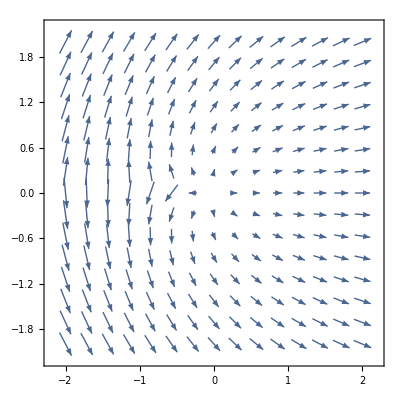

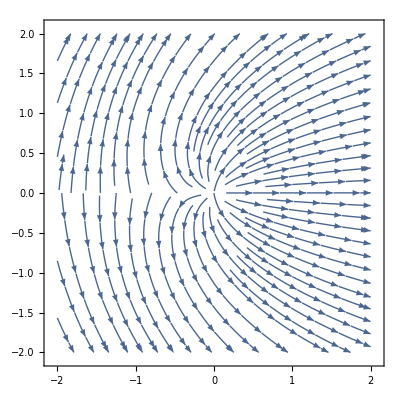

```mathematica
VectorPlot[{Re[ProductLog[x+ⅈ y]],Im[ProductLog[x+ⅈ y]]},{x,-2,2},{y,-2,2}]
StreamPlot[{Re[ProductLog[x+ⅈ y]],Im[ProductLog[x+ⅈ y]]},{x,-2,2},{y,-2,2}]
```

1+ProductLog[((R-T) (R+T))/ⅇ]

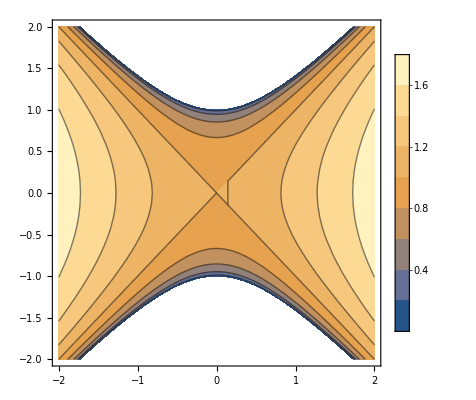

```mathematica
r/.slScKs
ContourPlot[%,{R,-2,2},{T,-2,2},RegionFunction->Function[{R,T},rgKs],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->Automatic]
```

Log[Abs[(R+T)/(R-T)]]

Power::infy: Infinite expression 1/0. encountered.

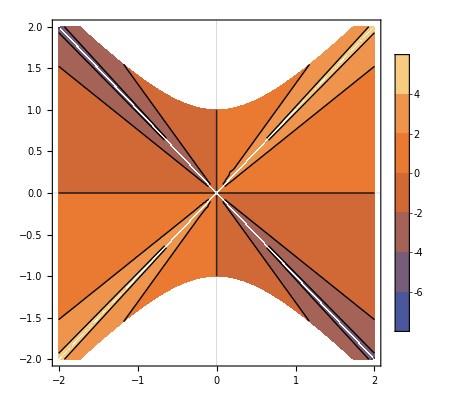

Log[(R-T) (R+T)]

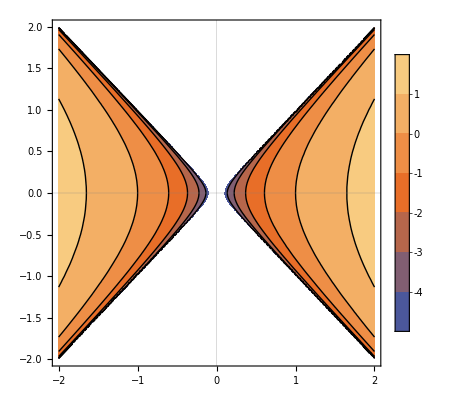

```mathematica
Log[Abs[ⅇ^t/.slScKs]]
(*T needs to consider the complex phase*)
ContourPlot[%,{R,-2,2},{T,-2,2},RegionFunction->Function[{R,T},rgKs],Exclusions->(R-T)(R+T)==0,AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->Automatic]
Log[ⅇ^rs/.slToKs]
(*so does rs*)
ContourPlot[%,{R,-2,2},{T,-2,2},RegionFunction->Function[{R,T},rgKs&&(R+T)(R-T)>0],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->Automatic]
```

-2 Log[R-T]

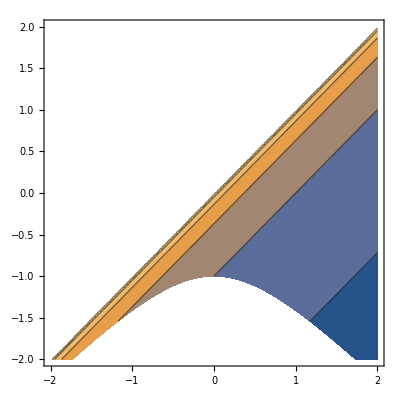

2 Log[R+T]

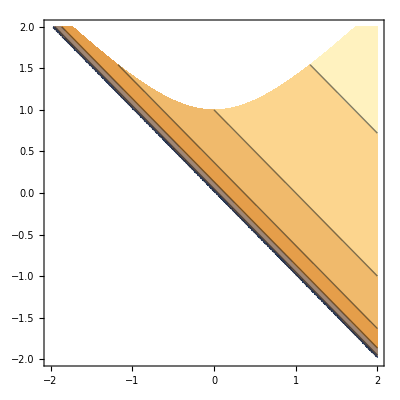

```mathematica
u/.slTlKs
ContourPlot[%,{R,-2,2},{T,-2,2},RegionFunction->Function[{R,T},rgKs&&R-T>0],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->Automatic]
v/.slTlKs
ContourPlot[%,{R,-2,2},{T,-2,2},RegionFunction->Function[{R,T},rgKs&&R+T>0],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->Automatic]
```

```mathematica
Solve[ProductLog[x]==0,x]
```

{{x→0}}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

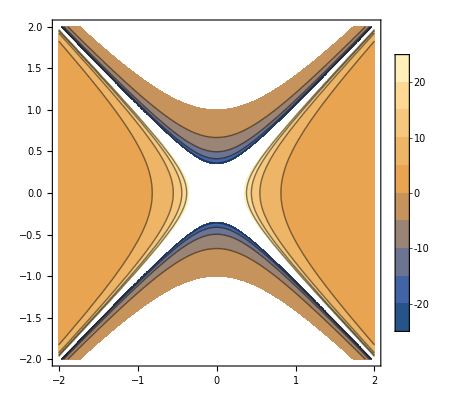

```mathematica
ContourPlot[1/ProductLog[((R-T) (R+T))/(ⅇ RS^2)],{R,-2,2},{T,-2,2},RegionFunction->Function[{R,T},rgKs],Exclusions->(R-T)(R+T)==0,PlotLegends->Automatic]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

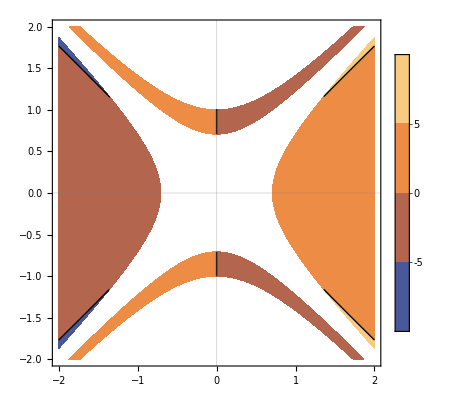

```mathematica
ContourPlot[pdrKs[[1]],{R,-2,2},{T,-2,2},RegionFunction->Function[{R,T},rgKs&&Abs[R^2-T^2]>1/2],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->Automatic]
```

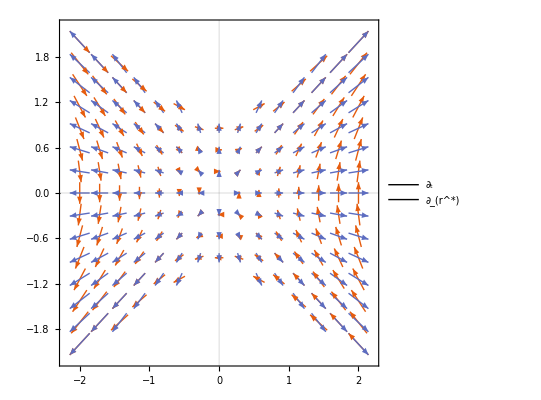

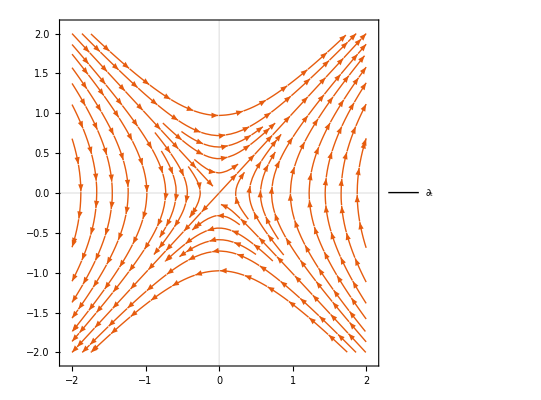

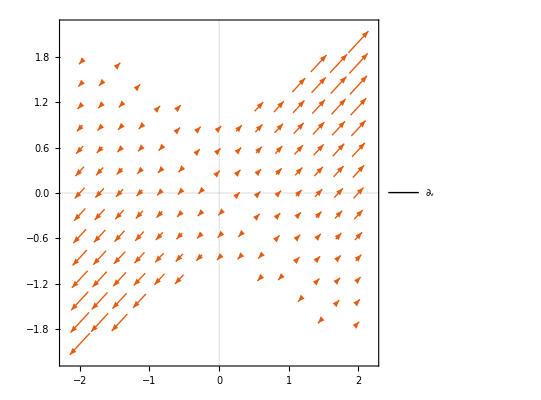

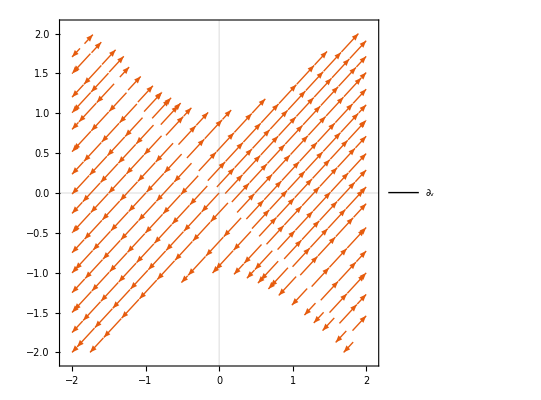

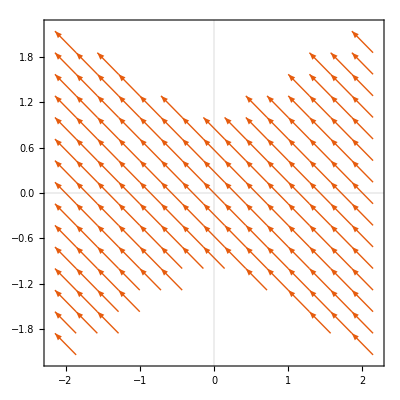

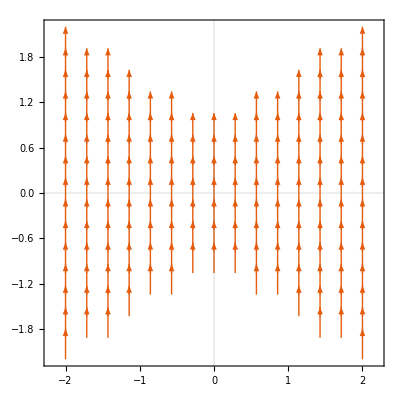

```mathematica
VectorPlot[{pdtKs,pdrsKs},{R,-2,2},{T,-2,2},RegionFunction->Function[{R,T},rgKs],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->{"∂_t ","∂_(r^*) "}]
StreamPlot[pdtKs,{R,-2,2},{T,-2,2},RegionFunction->Function[{R,T},rgKs],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->{"∂_t "}]
VectorPlot[pdvKs,{R,-2,2},{T,-2,2},RegionFunction->Function[{R,T},rgKs],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->{"∂_v "}]
StreamPlot[pdvKs,{R,-2,2},{T,-2,2},RegionFunction->Function[{R,T},rgKs],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->{"∂_v "}]
(*VectorPlot[pdrKs,{R,-2,2},{T,-2,2},RegionFunction->Function[{R,T},rgKs],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->Automatic]*)
VectorPlot[pdUKs,{R,-2,2},{T,-2,2},RegionFunction->Function[{R,T},rgKs],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->Automatic]
VectorPlot[{0,1},{R,-2,2},{T,-2,2},RegionFunction->Function[{R,T},rgKs],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->Automatic]
```

1+ProductLog[(1-(2 Cos[2 ρ])/(Cos[2 ρ]+Cos[2 τ]))/ⅇ]

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

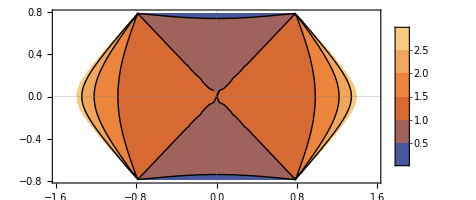

```mathematica
r/.slScCf
ContourPlot[%,{ρ,-π/2,π/2},{τ,-π/4,π/4},RegionFunction->Function[{ρ,τ},rgCf],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->Automatic]
```

Log[Abs[Cot[ρ-τ] Tan[ρ+τ]]]

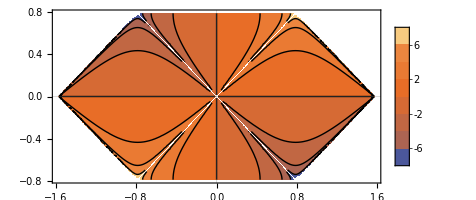

Log[Abs[Tan[ρ-τ] Tan[ρ+τ]]]

-Graphics-

```mathematica
Log[Abs[ⅇ^t/.slScCf]]
(*T needs to consider the complex phase*)
ContourPlot[%,{ρ,-π/2,π/2},{τ,-π/4,π/4},RegionFunction->Function[{ρ,τ},rgCf],Exclusions->(ρ-τ)(ρ+τ)==0,AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->Automatic]
Log[Abs[ⅇ^rs/.slToCf]]
(*so does rs*)
ContourPlot[%,{ρ,-π/2,π/2},{τ,-π/4,π/4},RegionFunction->Function[{ρ,τ},rgCf],Exclusions->(ρ-τ)(ρ+τ)==0,AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->Automatic]
```

```mathematica
u/.slTlCf
ContourPlot[%,{ρ,-π/2,π/2},{τ,-π/4,π/4},RegionFunction->Function[{ρ,τ},rgCf&&ρ-τ>0],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->Automatic]
v/.slTlCf
ContourPlot[%,{ρ,-π/2,π/2},{τ,-π/4,π/4},RegionFunction->Function[{ρ,τ},rgCf&&ρ+τ>0],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->Automatic]
```

-2 Log[Tan[ρ-τ]]

-Graphics-

2 Log[Tan[ρ+τ]]

-Graphics-

```mathematica
VectorPlot[pdrCf,{ρ,-π/2,π/2},{τ,-π/4,π/4},RegionFunction->Function[{ρ,τ},rgCf],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->{"∂_r "}]
VectorPlot[{pdtCf,pdrsCf},{ρ,-π/2,π/2},{τ,-π/4,π/4},RegionFunction->Function[{ρ,τ},rgCf],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->{"∂_t ","∂_(r^*) "}]
VectorPlot[pdTCf,{ρ,-π/2,π/2},{τ,-π/4,π/4},RegionFunction->Function[{ρ,τ},rgCf],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->Automatic]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
VectorPlot[{pdvCf},{ρ,-π/2,π/2},{τ,-π/4,π/4},RegionFunction->Function[{ρ,τ},rgCf],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->{"∂_v "}]
VectorPlot[{pdUCf},{ρ,-π/2,π/2},{τ,-π/4,π/4},RegionFunction->Function[{ρ,τ},rgCf],AspectRatio->Automatic,PlotTheme->"Scientific",PlotLegends->{"∂_U "}]
```

-Graphics-

-Graphics-

```mathematica
(*ClearAll[RS]*)
```